```mathematica
ClearAll["Global`*"]
wd=SetDirectory@NotebookDirectory[];


e1=Take[Import[wd<>"/../../output/e_1.000.dat"]][[All,{1,2,4}]];
e2=Take[Import[wd<>"/../../output/e_1.500.dat"]][[All,{1,2,4}]];
e3=Take[Import[wd<>"/../../output/e_2.000.dat"]][[All,{1,2,4}]];
e4=Take[Import[wd<>"/../../output/e_2.500.dat"]][[All,{1,2,4}]];
e5=Take[Import[wd<>"/../../output/e_3.000.dat"]][[All,{1,2,4}]];
e6=Take[Import[wd<>"/../../output/e_3.500.dat"]][[All,{1,2,4}]];

plpt1=Take[Import[wd<>"/../../output/plpt_1.000.dat"]][[All,{1,2,4}]];
plpt2=Take[Import[wd<>"/../../output/plpt_1.500.dat"]][[All,{1,2,4}]];
plpt3=Take[Import[wd<>"/../../output/plpt_2.000.dat"]][[All,{1,2,4}]];
plpt4=Take[Import[wd<>"/../../output/plpt_2.500.dat"]][[All,{1,2,4}]];
plpt5=Take[Import[wd<>"/../../output/plpt_3.000.dat"]][[All,{1,2,4}]];
plpt6=Take[Import[wd<>"/../../output/plpt_3.500.dat"]][[All,{1,2,4}]];

ux1=Take[Import[wd<>"/../../output/ux_1.000.dat"]][[All,{1,2,4}]];
ux2=Take[Import[wd<>"/../../output/ux_1.500.dat"]][[All,{1,2,4}]];
ux3=Take[Import[wd<>"/../../output/ux_2.000.dat"]][[All,{1,2,4}]];
ux4=Take[Import[wd<>"/../../output/ux_2.500.dat"]][[All,{1,2,4}]];
ux5=Take[Import[wd<>"/../../output/ux_3.000.dat"]][[All,{1,2,4}]];
ux6=Take[Import[wd<>"/../../output/ux_3.500.dat"]][[All,{1,2,4}]];

aL1=Take[Import[wd<>"/../../output/aL_1.000.dat"]][[All,{1,2,4}]];
aL2=Take[Import[wd<>"/../../output/aL_1.500.dat"]][[All,{1,2,4}]];
aL3=Take[Import[wd<>"/../../output/aL_2.000.dat"]][[All,{1,2,4}]];
aL4=Take[Import[wd<>"/../../output/aL_2.500.dat"]][[All,{1,2,4}]];
aL5=Take[Import[wd<>"/../../output/aL_3.000.dat"]][[All,{1,2,4}]];
aL6=Take[Import[wd<>"/../../output/aL_3.500.dat"]][[All,{1,2,4}]];
```

```mathematica
(*max = 6.0001;*)
max=1.0;

dx= 0.05;
xpts=201;

s1=1+xpts*(xpts-1)/2;
s2=xpts*(1+(xpts-1)/2);
```

```mathematica
pts=1/dx;

DarkBlueBlueBlend=Table[Blend[{Darker[Blue],Blue},dx*i],{i,0,pts-1}];
BlueCyanBlend=Table[Blend[{Blue,Cyan},dx*i],{i,0,pts-1}];
CyanGreenBlend=Table[Blend[{Cyan,Green},dx*i],{i,0,pts-1}];
GreenYellowBlend=Table[Blend[{Green,Yellow},dx*i],{i,0,pts-1}];
YellowOrangeBlend=Table[Blend[{Yellow,Orange},dx*i],{i,0,pts-1}];
OrangeRedBlend=Table[Blend[{Orange,Red},dx*i],{i,0,pts-1}];
RedDarkRedBlend=Table[Blend[{Red,Darker[Red]},dx*i],{i,0,pts}];

colors=Flatten[{DarkBlueBlueBlend, BlueCyanBlend, CyanGreenBlend, GreenYellowBlend, YellowOrangeBlend, OrangeRedBlend,RedDarkRedBlend}];

colorpts=Table[1.0*i/(Length[colors]-1),{i,0,Length[colors]-1}];

Unprotect[ColorData];
ColorData["Jet"]=Function[x,Blend[Transpose[{colorpts,colors}],x / max]];
Protect[ColorData];

BarLegend[{ColorData["Jet"],{0,max}},LegendMarkerSize->300,LabelStyle->{FontSize->13,FontFamily->"Arial",Black}]
```

```mathematica
emax=Max[e1[[1;;All,3]]];

(* Gubser solution *)
q=1.0;
κ[τ_,r_]:=ArcTanh[(2.0*q^2*τ*Abs[r])/(1.0+q^2*(τ^2+r^2))];
ux[τ_,r_]:=Sinh[κ[τ,r]]*Sign[r];


e1test=Take[Import[wd<>"/gubser_data/e_1.000.dat"]];
e2test=Take[Import[wd<>"/gubser_data/e_1.500.dat"]];
e3test=Take[Import[wd<>"/gubser_data/e_2.000.dat"]];
e4test=Take[Import[wd<>"/gubser_data/e_2.500.dat"]];
e5test=Take[Import[wd<>"/gubser_data/e_3.000.dat"]];
e6test=Take[Import[wd<>"/gubser_data/e_3.500.dat"]];

plpt1test=Take[Import[wd<>"/gubser_data/plpt_1.000.dat"]];
plpt2test=Take[Import[wd<>"/gubser_data/plpt_1.500.dat"]];
plpt3test=Take[Import[wd<>"/gubser_data/plpt_2.000.dat"]];
plpt4test=Take[Import[wd<>"/gubser_data/plpt_2.500.dat"]];
plpt5test=Take[Import[wd<>"/gubser_data/plpt_3.000.dat"]];
plpt6test=Take[Import[wd<>"/gubser_data/plpt_3.500.dat"]];

aL1test=Take[Import[wd<>"/gubser_data/aL_1.000.dat"]];
aL2test=Take[Import[wd<>"/gubser_data/aL_1.500.dat"]];
aL3test=Take[Import[wd<>"/gubser_data/aL_2.000.dat"]];
aL4test=Take[Import[wd<>"/gubser_data/aL_2.500.dat"]];
aL5test=Take[Import[wd<>"/gubser_data/aL_3.000.dat"]];
aL6test=Take[Import[wd<>"/gubser_data/aL_3.500.dat"]];

ux1test=Table[{-5.0 +i*dx,ux[1.0,-5.0+i*dx]},{i,0,xpts-1}];
ux2test=Table[{-5.0 +i*dx,ux[1.5,-5.0+i*dx]},{i,0,xpts-1}];
ux3test=Table[{-5.0 +i*dx,ux[2.0,-5.0+i*dx]},{i,0,xpts-1}];
ux4test=Table[{-5.0 +i*dx,ux[2.5,-5.0+i*dx]},{i,0,xpts-1}];
ux5test=Table[{-5.0 +i*dx,ux[3.0,-5.0+i*dx]},{i,0,xpts-1}];
ux6test=Table[{-5.0 +i*dx,ux[3.5,-5.0+i*dx]},{i,0,xpts-1}];


(*****************************************)


e1slice=e1[[s1;;s2,{1,3}]];
e2slice=e2[[s1;;s2,{1,3}]];
e3slice=e3[[s1;;s2,{1,3}]];
e4slice=e4[[s1;;s2,{1,3}]];
e5slice=e5[[s1;;s2,{1,3}]];
e6slice=e6[[s1;;s2,{1,3}]];

plpt1slice=plpt1[[s1;;s2,{1,3}]];
plpt2slice=plpt2[[s1;;s2,{1,3}]];
plpt3slice=plpt3[[s1;;s2,{1,3}]];
plpt4slice=plpt4[[s1;;s2,{1,3}]];
plpt5slice=plpt5[[s1;;s2,{1,3}]];
plpt6slice=plpt6[[s1;;s2,{1,3}]];


ux1slice=ux1[[s1;;s2,{1,3}]];
ux2slice=ux2[[s1;;s2,{1,3}]];
ux3slice=ux3[[s1;;s2,{1,3}]];
ux4slice=ux4[[s1;;s2,{1,3}]];
ux5slice=ux5[[s1;;s2,{1,3}]];
ux6slice=ux6[[s1;;s2,{1,3}]];

aL1slice=aL1[[s1;;s2,{1,3}]];
aL2slice=aL2[[s1;;s2,{1,3}]];
aL3slice=aL3[[s1;;s2,{1,3}]];
aL4slice=aL4[[s1;;s2,{1,3}]];
aL5slice=aL5[[s1;;s2,{1,3}]];
aL6slice=aL6[[s1;;s2,{1,3}]];


magentaTran={Blend[{Red,Magenta},0.5],AbsoluteThickness[2],Opacity[0.3]};
redTran={Red,AbsoluteThickness[2],Opacity[0.3]};
orangeTran={Blend[{Red,Orange},0.75],AbsoluteThickness[2],Opacity[0.3]};
greenTran={Blend[{Blue,Green},0.875],AbsoluteThickness[2],Opacity[0.3]};
blueTran={Blue,AbsoluteThickness[2],Opacity[0.3]};
cyanTran={Blend[{Blue,Cyan},0.75],AbsoluteThickness[2],Opacity[0.3]};
blueTran={Blue,AbsoluteThickness[2],Opacity[0.3]};
purplpteTran={Blend[{Blue,Purple},0.75],AbsoluteThickness[2],Opacity[0.3]};

magenta={Blend[{Red,Magenta},0.5],AbsoluteDashing[{8,8}],AbsoluteThickness[2]};
red={Red,AbsoluteDashing[{8,8}],AbsoluteThickness[2]};
orange={Blend[{Red,Orange},0.75],AbsoluteDashing[{8,8}],AbsoluteThickness[2]};
green={Blend[{Blue,Green},0.875],AbsoluteDashing[{8,8}],AbsoluteThickness[2]};
cyan={Blend[{Blue,Cyan},0.75],AbsoluteDashing[{8,8}],AbsoluteThickness[2]};
blue={Blue,AbsoluteDashing[{8,8}],AbsoluteThickness[2]};
purplpte={Blend[{Blue,Purple},0.75],AbsoluteDashing[{8,8}],AbsoluteThickness[2]};

style={magentaTran,redTran,orangeTran,greenTran,cyanTran,blueTran,magenta,red,orange,green,cyan, blue};
```

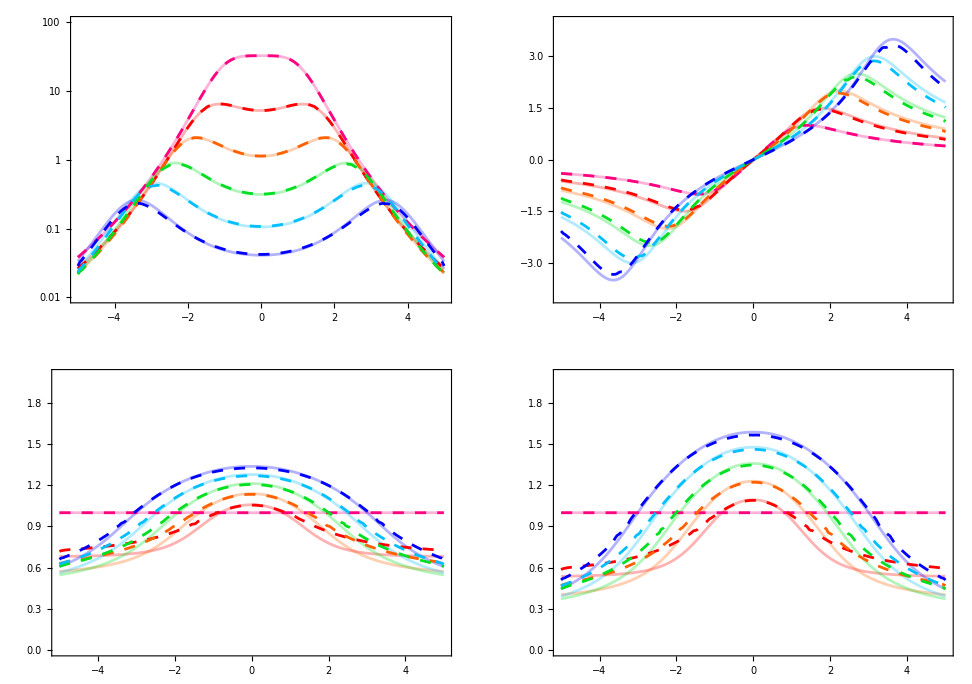

```mathematica
GraphicsGrid[{{
ListLogPlot[{e1test,e2test,e3test,e4test,e5test,e6test,e1slice,e2slice,e3slice,e4slice,e5slice,e6slice},Joined->True,InterpolationOrder->2,PlotRange->{{-5,5},{0.01,100}},PlotStyle->style,Frame->True,FrameStyle->Black,Axes->None,BaseStyle->{FontSize->13,FontFamily->"Arial"},AspectRatio->0.7,ImageSize->450],

ListPlot[{ux1test,ux2test,ux3test,ux4test,ux5test,ux6test,ux1slice,ux2slice,ux3slice,ux4slice,ux5slice,ux6slice},Joined->True,InterpolationOrder->2,PlotRange->{{-5,5},{-4,4}},PlotStyle->style,Frame->True,FrameStyle->Black,Axes->None,BaseStyle->{FontSize->13,FontFamily->"Arial"},AspectRatio->0.7,ImageSize->450]},

{ListPlot[{aL1test,aL2test,aL3test,aL4test,aL5test,aL6test,aL1slice,aL2slice,aL3slice,aL4slice,aL5slice,aL6slice},Joined->True,InterpolationOrder->2,PlotRange->{{-5,5},{0.,2}},PlotStyle->style,Frame->True,FrameStyle->Black,Axes->None,BaseStyle->{FontSize->13,FontFamily->"Arial"},AspectRatio->0.7,ImageSize->450],

ListPlot[{plpt1test,plpt2test,plpt3test,plpt4test,plpt5test,plpt6test,plpt1slice,plpt2slice,plpt3slice,plpt4slice,plpt5slice,plpt6slice},Joined->True,InterpolationOrder->2,PlotRange->{{-5,5},{0.,2.0}},PlotStyle->style,Frame->True,FrameStyle->Black,Axes->None,BaseStyle->{FontSize->13,FontFamily->"Arial"},AspectRatio->0.7,ImageSize->450]}}]

Export[wd<>"/gubser_usual_test.pdf",%];
```

```mathematica
(* PL Matching *)
```

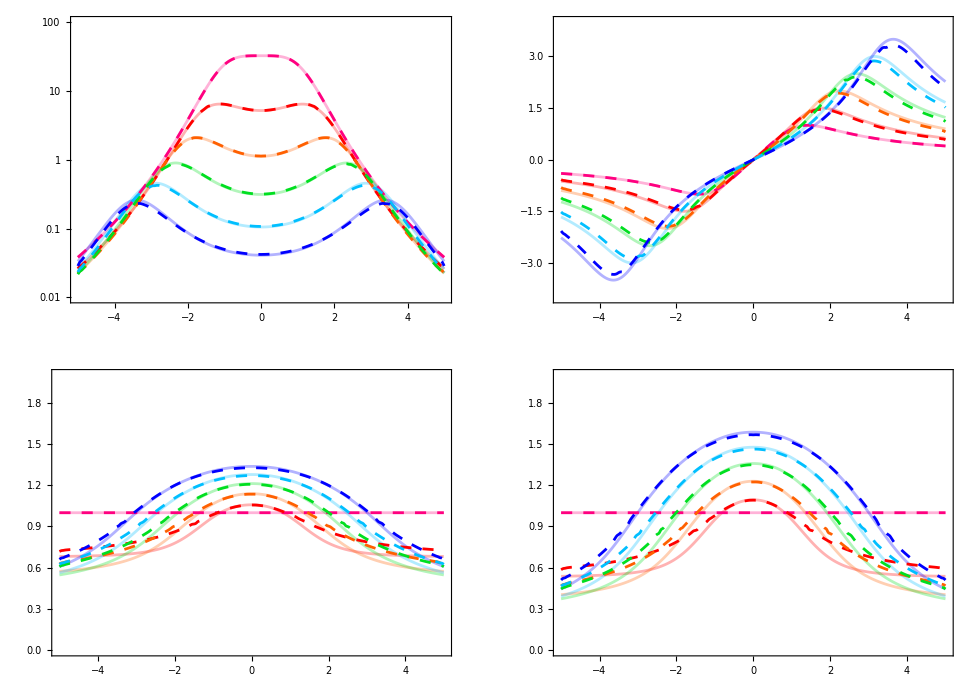
```mathematica
-Graphics-;
```